```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
MemoryInUse[](*useful function when using many scatterers!*)
```

52901888

```mathematica
Names["MultipleScattering2D`*"]
```

{AttenuationFromListFrequency,CombineWaves,ConvolutionTest,CylindricalWaveFromCoefficients,DrawScatterers,ExportListCylindricalWave,ExportListFrequency,ExportListWaves,FrequencyFromScatterers,GenerateParticles,ImportBoundaryFrequency,ImportListCylindricalWave,ImportListFrequency,ImportListWaves,ListCylindricalWaveDueToImpulse,ListenersOutsideScatterers,ListPlotSequence,ListWavesDueToImpulse,MultipleScatteringCoefficients,OutWave,PlotCylindricalWave,rngωFourierOffset,ScatteringCoefficientOperator,SetParametersAndReturnOptions,SingleScattererCoefficientsFromImpulse,StatsFromParticles,TotalWave}

## Diffraction from a large cylinder

```mathematica
(*radius of the scatterers*)
radius=10.; 
(*max number of hankel functions per scatterer*)
N0=6;
(*angular frequency*)
ωs = {2.};

options={
"ImpulsePosition"-> {0,0},
"SourceWave"->(I/4 HankelH1[0,#2 Norm[{#1[[1]],#1[[2]]}] /.Abs->Identity]&),(*chose 2D greens*)
"BoundaryCondition"-> "Dirchlett"(*"BoundaryCondition"-> "Neumann"*)
};

(*Position of the scatterers and listeners/recievers*)
Xs={{0,15}};
```

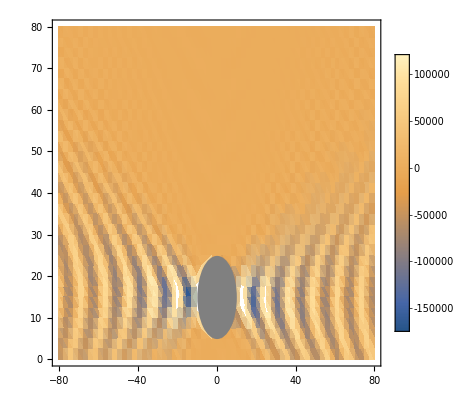

/home/art-man/Software/Dropbox (The University of Manchester)/study/Scattering/MultipleScattering2D/v3/examples/../media/BugCylinderDiffraction.pdf

```mathematica
(*choose mesh*)
	rngX=Range[-8 radius,8 radius,radius/4];
	rngY=Range[0.,8 radius,radius/4];
         listeners = ListenersOutsideScatterers[radius,Xs,rngX,rngY];
(*Calculate response at every mesh point *)
	responses =FrequencyFromScatterers[listeners, Xs,radius, N0,ωs];
(*plot the real part of the result*)
data = Flatten@{listeners[[#]],Re@responses[[#,1,2]]}&/@Range[Length@responses];
	p1=ListDensityPlot[data,InterpolationOrder->1,PlotLegends->Automatic ];
	p2 = DrawScatterers[Xs,radius];
	p =Show[p1,p2,AspectRatio-> Automatic]
Export[NotebookDirectory[]<>"../media/BugCylinderDiffraction.pdf",p]
```